```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Parameters

```mathematica
A=197;
r0=6.38;(*fm*)
R=5r0;(*fm*)
a0=0.535 ;(*fm*)
σ=6.5;(*fm^2=mb/10, at √s=2.76TeV*)
d=√(σ/π)
```

1.43841

## Define functions

```mathematica
ρ0=1/NIntegrate[4π r^2 1/(1+Exp[(r-r0)/a0]),{r,0,∞}];
ws[r_]:=ρ0/(1+Exp[(r-r0)/a0]);
spherdiff[r_,r1_,θ_,θ1_,ϕ_,ϕ1_]:=√(r^2+r1^2-2 r r1(Sin[θ]Sin[θ1]Cos[ϕ-ϕ1]+Cos[θ]Cos[θ1]));
```

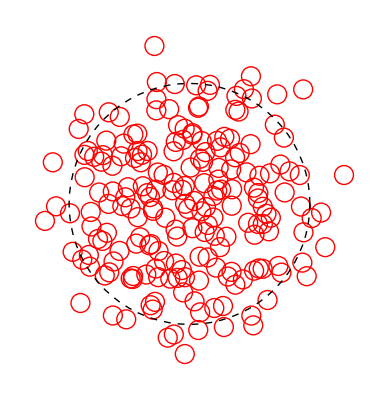

```mathematica
coords={};
SetSharedVariable[coords];
Module[{r,θ,i=0,rM,ϕ,ii,dup},While[Length[coords]<A,rM=RandomVariate[NormalDistribution[6,2]];
r=RandomReal[]R ;
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
dup=0;
For[ii=1,ii≤Length[coords],ii++,If[spherdiff[r,coords[[ii,1]],θ,coords[[ii,2]],ϕ,coords[[ii,3]]]≤d,dup+=1]];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(rM-6)^2)/(2 2^2)]) &&dup==0,coords=Append[coords,{r,θ,ϕ}]];i++];];
Graphics[{Table[{Red,Circle[{coords[[i,1]]Cos[coords[[i,3]]]Sin[coords[[i,2]]],coords[[i,1]]Sin[coords[[i,3]]]Sin[coords[[i,2]]]},0.5]},{i,1,A,1}],{Dashed,Circle[{0,0},r0]}}]
```

```mathematica
glauberMCcollcoords[impact_]:=Module[{b=impact,coords1={},coords2={},r,θ,ϕ,i=0,collcoords={},dup1,dup2},
While[Length[coords1]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
dup1=0;
For[ii=1,ii≤Length[coords1],ii++,If[spherdiff[r,coords1[[ii,1]],θ,coords1[[ii,2]],ϕ,coords1[[ii,3]]]≤d,dup1+=1]];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)])&&dup1==0 ,coords1=Append[coords1,{r,θ,ϕ}]];i++];
While[Length[coords2]<A,
r=RandomVariate[NormalDistribution[6,2]];
θ=ArcCos[2 RandomReal[]-1];
ϕ=2π RandomReal[];
dup2=0;
For[ii=1,ii≤Length[coords2],ii++,If[spherdiff[r,coords2[[ii,1]],θ,coords2[[ii,2]],ϕ,coords2[[ii,3]]]≤d,dup2+=1]];
If[RandomReal[]<4π r^2 ws[r]/(2 1/(√(2π 2^2))Exp[(-(r-6)^2)/(2 2^2)])&&dup2==0 ,coords2=Append[coords2,{r,θ,ϕ}]];i++];
coords1=coords1/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]+b/2,a Sin[phi]Sin[th]};
coords2=coords2/.{a_,th_,phi_}:>{a Cos[phi]Sin[th]-b/2,a Sin[phi]Sin[th]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,collcoords=Append[Append[collcoords,coords1[[i]]],coords2[[ii]]];],{ii,1,A},{i,1,A}];
Return[collcoords]];
```

```mathematica
gauss[x_,x1_,y_,y1_,r_]:=Exp[-((x-x1)^2+(y-y1)^2)/(2 r^2)];
sumgauss[x_,y_,r_,collcoords_]:=Sum[gauss[x,collcoords[[i,1]],y,collcoords[[i,2]],r],{i,Length[collcoords]}];
```

```mathematica
endenTab[impact_,r_,n_]:=Flatten[ParallelTable[{{x,y},1/n Sum[sumgauss[x,y,r,glauberMCcollcoords[impact]],{i,1,n}]},{x,-6,6,1},{y,-6,6,1}],1];
```

## Results

### Output

```mathematica
enden0=endenTab[0,0.5,100];//AbsoluteTiming
```

{10860.1,Null}

```mathematica
enden5=endenTab[5,0.5,100];//AbsoluteTiming
```

{6555.18,Null}

```mathematica
enden10=endenTab[10,0.5,100];//AbsoluteTiming
```

$Aborted

```mathematica
Export["spectraldata/GlauberInit/enden0.dat",enden0];
Export["spectraldata/GlauberInit/enden5.dat",enden5];
```

```mathematica
Export["spectraldata/GlauberInit/enden10.dat",enden10];
```

### Input

```mathematica
enden0=ToExpression[Import["spectraldata/GlauberInit/enden0.dat","TSV"]];
enden5=ToExpression[Import["spectraldata/GlauberInit/enden5.dat","TSV"]];
```

```mathematica
enden0inter=Interpolation[enden0];
enden5inter=Interpolation[enden5];
```

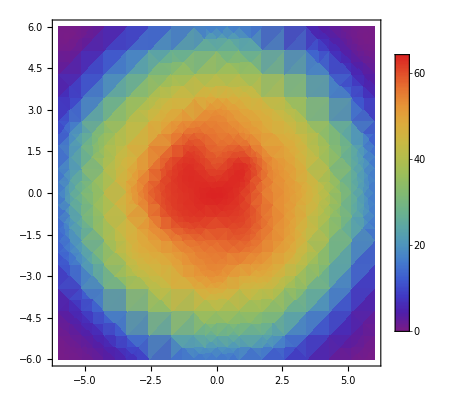

```mathematica
DensityPlot[enden0inter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

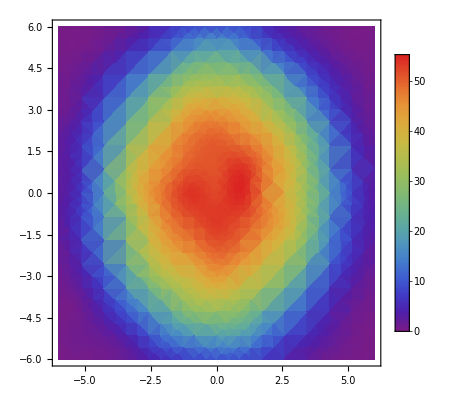

```mathematica
DensityPlot[enden5inter[x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

### Parameterization

#### b = 0

```mathematica
endendiag0={};
endenx0={};
Do[If[enden0[[i,1,1]]==enden0[[i,1,2]],endendiag0=Append[endendiag0,{enden0[[i,1,1]],enden0[[i,2]]}]],{i,Length[enden0]}]
Do[If[enden0[[i,1,2]]==0,endenx0=Append[endenx0,{enden0[[i,1,1]],enden0[[i,2]]}]],{i,Length[enden0]}]
```

```mathematica
fitdiag0=NonlinearModelFit[endendiag0,a Exp[-b x^2],{a,b},x];
fitx0=NonlinearModelFit[endenx0,a Exp[-b x^2],{a,b},x];
```

```mathematica
fitdiag0["BestFitParameters"]
fitx0["BestFitParameters"]
```

{a→67.7964,b→0.0779838}

{a→65.9141,b→0.0333833}

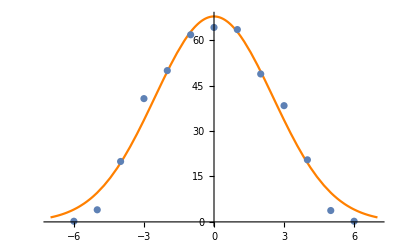

```mathematica
Show[Plot[fitdiag0[x],{x,-7,7},PlotStyle->Orange],ListPlot[endendiag0]]
```

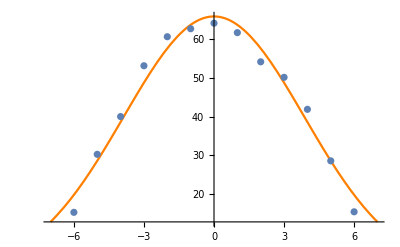

```mathematica
Show[Plot[fitx0[x],{x,-7,7},PlotStyle->Orange],ListPlot[endenx0]]
```

```mathematica
endenx0par[x_]:=Exp[-0.03338328309135508 x^2]
```

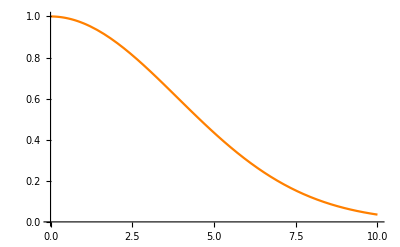

```mathematica
Plot[endenx0par[x],{x,0,10},PlotStyle->Orange]
```

#### b = 5

```mathematica
endeny5={};
endenx5={};
Do[If[enden5[[i,1,1]]==0,endeny5=Append[endeny5,{enden5[[i,1,2]],enden5[[i,2]]}]],{i,Length[enden5]}]
Do[If[enden5[[i,1,2]]==0,endenx5=Append[endenx5,{enden5[[i,1,1]],enden5[[i,2]]}]],{i,Length[enden5]}]
```

```mathematica
fity5=NonlinearModelFit[endeny5,a Exp[-b x^2],{a,b},x];
fitx5=NonlinearModelFit[endenx5,a Exp[-b x^2],{a,b},x];
```

```mathematica
fity5["BestFitParameters"]
fitx5["BestFitParameters"]
```

{a→56.4132,b→0.0382282}

{a→58.0635,b→0.0618208}

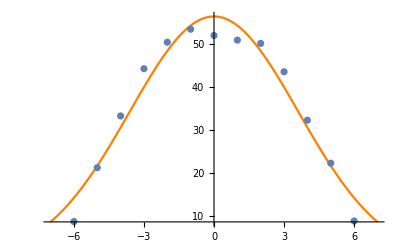

```mathematica
Show[Plot[fity5[y],{y,-7,7},PlotStyle->Orange],ListPlot[endeny5]]
```

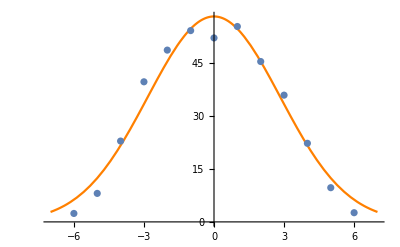

```mathematica
Show[Plot[fitx5[x],{x,-7,7},PlotStyle->Orange],ListPlot[endenx5]]
```

```mathematica
endenx5par[x_]:=Exp[-0.061820788290272606 x^2]
endeny5par[y_]:=Exp[-0.03822821785757879 y^2]
```

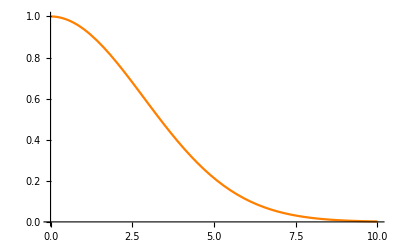

```mathematica
Plot[endenx5par[x],{x,0,10},PlotStyle->Orange]
```

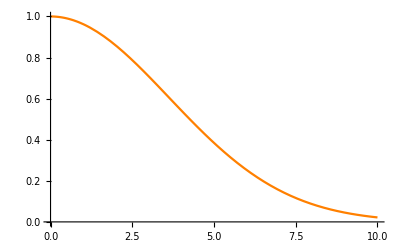

```mathematica
Plot[endeny5par[x],{x,0,10},PlotStyle->Orange]
```

## Modified potential

### 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

### Plots

```mathematica
kfinal={0.4709613222916442,-0.2550225519531524};
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c;
mDcalx0[μ_,T_,c_,d_,r_]:=(Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ])endenx0par[r];
mDcalx5[μ_,T_,c_,d_,r_]:=(Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ])endenx5par[r];
Vsb[r_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](c-α/r+σ r)+HeavisideTheta[r-1.25/0.197](c-α/(1.25/0.197)+σ 1.25/0.197);
ReVsb[r_,m_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c)+HeavisideTheta[r-1.25/0.197]ReV[1.25/0.197,m,α,σ,c];
ReVsbmDx0[r_,m_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c)+HeavisideTheta[r-1.25/0.197]ReV[1.25/0.197,mDcalx0[2π,T,kfinal[[1]],kfinal[[2]],1.25/0.197],α,σ,c];
ReVsbmDx5[r_,m_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c)+HeavisideTheta[r-1.25/0.197]ReV[1.25/0.197,mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],1.25/0.197],α,σ,c];
```

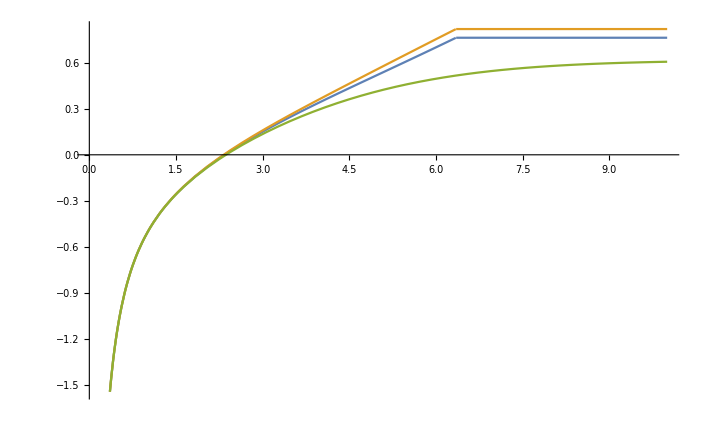

```mathematica
T=0.155;
Plot[{ReVsbmDx0[r,mDcalx0[2π,T,kfinal[[1]],kfinal[[2]],r],αcont[[1]],σcont[[1]],ccont[[1]]],ReVsbmDx5[r,mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],r],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r,mDcal[2π,T,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,10}]
```

## Generate spectral functions

```mathematica
R=20000;
Mc=1.4690612135716832;
Mb=4.882;
```

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞},PrecisionGoal->2]];
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

### b = 0

```mathematica
ϵ=1/1000;
ϕ1table=Quiet[ParallelTable[{x,1-ϕ[mDcalx0[2π,T,kfinal[[1]],kfinal[[2]],x]x]},{x,ϵ/100,20,10ϵ}]];
```

$Aborted

```mathematica
N[ϕ1table[[1039]]]
```

{10.38,0.00823418}

```mathematica
N[ϕ1table[[-1]]]
```

{20.,6.06294×10^-11}

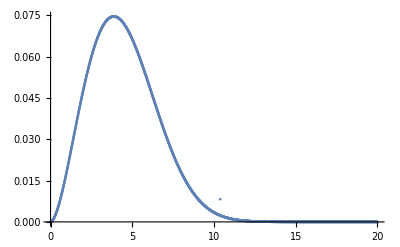

```mathematica
ListPlot[ϕ1table]
```

```mathematica
ϕ1fit=NonlinearModelFit[ϕ1table,a x^2 Exp[-b (x-c)^2],{a,b,c},x];
```

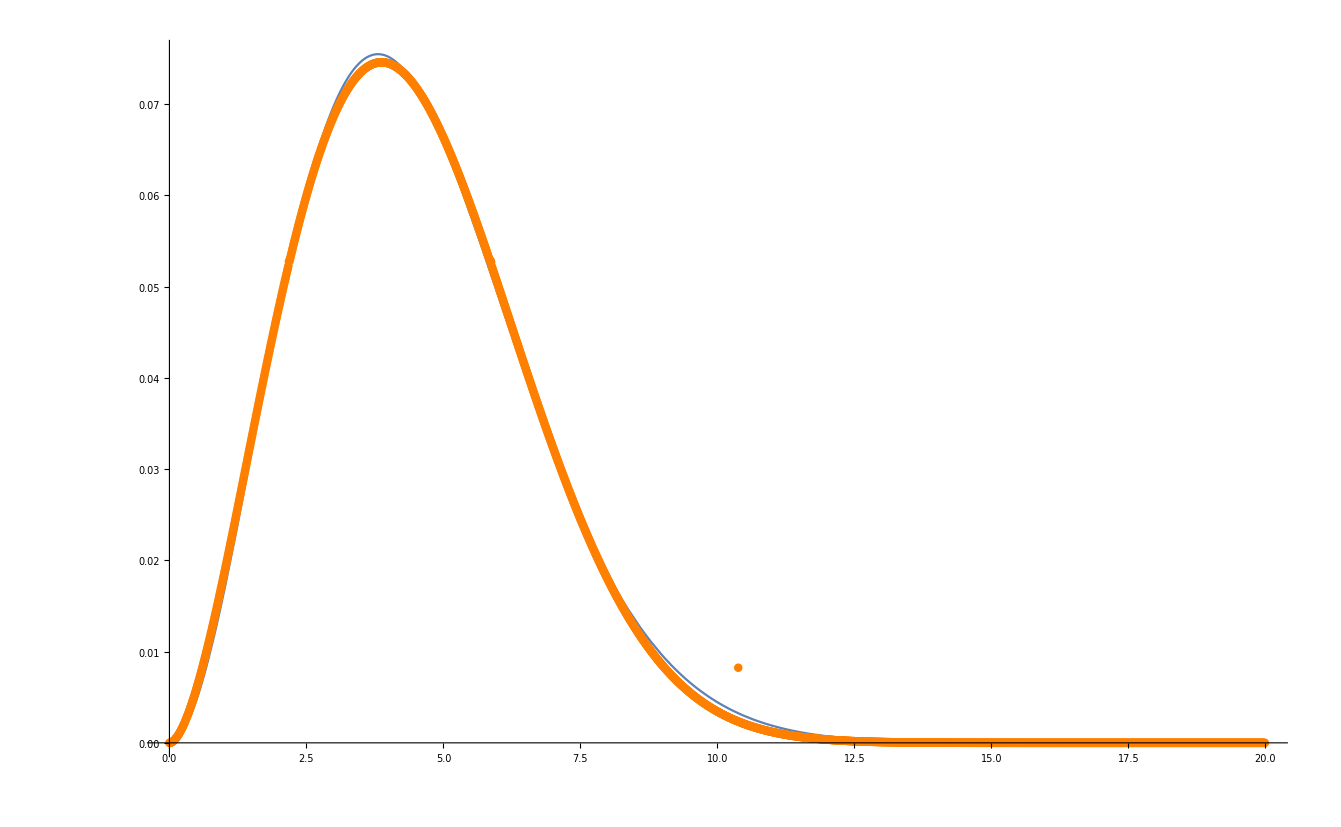

```mathematica
Show[Plot[ϕ1fit[x],{x,0,20}],ListPlot[ϕ1table,PlotStyle->Orange]]
```

```mathematica
μ[r_]:=(mDcalx0[2π,0.155,kfinal[[1]],kfinal[[2]],r]^2 σcont[[1]]/αcont[[1]])^(1/4);
r1[r_]:=mDcalx0[2π,0.155,kfinal[[1]],kfinal[[2]],r]/μ[r];
pg=1;
c1[r_]:=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]]
ψ1[x_,r_]:=c1[r]-ParabolicCylinderR[μ[x] x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg,Method->"GlobalAdaptive",MaxRecursion->20]-Re[ParabolicCylinderI[μ[x] x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg,Method->"GlobalAdaptive",MaxRecursion->20];
```

```mathematica
ψ1tab=ParallelTable[{x,Quiet[ψ1[x,r1[x]]]},{x,0,20,0.1}];
```

```mathematica
ListPlot[ψ1tab,PlotRange->All]
```

-Graphics-

```mathematica
ψ1fit=NonlinearModelFit[ψ1tab,a x^2 Exp[-b (x-c)^2],{a,b,c},x];
```

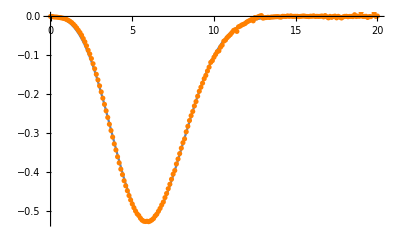

```mathematica
Show[Plot[ψ1fit[x],{x,0,20}],ListPlot[ψ1tab,PlotStyle->Orange]]
```

```mathematica
swaveccspectrab0x:=Module[{T=0.155,σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,Tstring},
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
V[x_]:=ReVsbmDx0[x,mDcalx0[2π,T,kfinal[[1]],kfinal[[2]],x],α,σ,c]+ⅈ (α T ϕ1[x]+α T ψ1fit[x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/ccswb0xspectra.dat",ccsT]
]
```

```mathematica
swaveccspectrab0x//AbsoluteTiming
```

$Aborted

### b = 5

```mathematica
ϵ=1/1000;
ϕ1table5=Quiet[Join[Parallelize[Table[{x,1-ϕ[mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x]x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x]x]},{x,2+100ϵ,10,100ϵ}]],Parallelize[Table[{x,Abs[1-ϕ[mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x]x]]},{x,10+1000ϵ,100,10000ϵ}]],Parallelize[Table[{x,Abs[1-ϕ[mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x]x]]},{x,100+100000ϵ,10000,100000ϵ}]],Parallelize[Table[{x,1-ϕ[mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x]x]},{x,10000+10000000ϵ,1000000,10000000ϵ}]]]];//AbsoluteTiming
```

$Aborted

```mathematica
μ5[r_]:=(mDcalx5[2π,0.155,kfinal[[1]],kfinal[[2]],r]^2 σcont[[1]]/αcont[[1]])^(1/4);
r15[r_]:=mDcalx5[2π,0.155,kfinal[[1]],kfinal[[2]],r]/μ[r];
pg=1;
c15[r_]:=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]]
ψ15[x_,r_]:=c1[r]-ParabolicCylinderR[x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg,Method->"GlobalAdaptive",MaxRecursion->20]-Re[ParabolicCylinderI[x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg,Method->"GlobalAdaptive",MaxRecursion->20];
```

```mathematica
ψ1tab5=ParallelTable[{x,Quiet[ψ15[μ5[x]x,r15[x]]]},{x,0,20,0.5}];
```

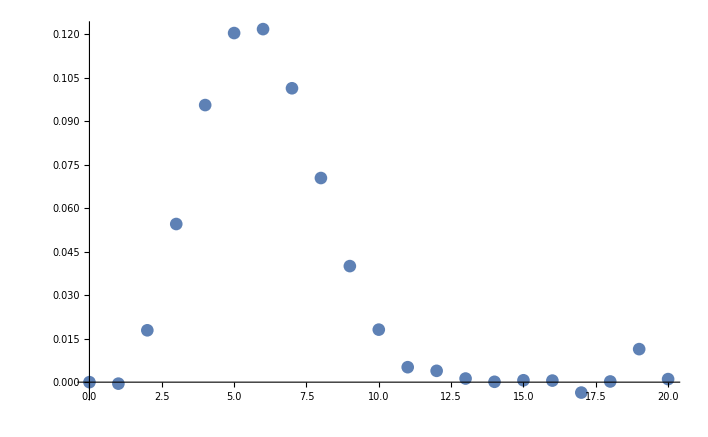

```mathematica
ListPlot[ψ1tab5,PlotRange->All]
```

```mathematica
ψ1fit5=NonlinearModelFit[ψ1tab5,a x Exp[-b (x-c)^2],{a,b,c},x];
```

FittedModel[0.0240863 ⅇ^(-0.0946842 (-4.7192+x)^2) x]

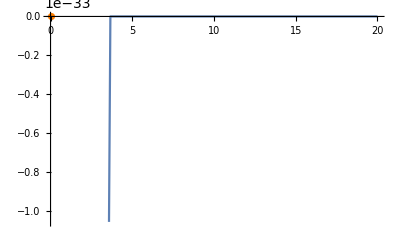

```mathematica
Show[Plot[ψ1fit[x],{x,0,20}],ListPlot[ψ1tab,PlotStyle->Orange]]
```

```mathematica
swaveccspectrab5x:=Module[{T=0.155,σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,Tstring},
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
V[x_]:=ReVsbmDx0[x,mDcalx5[2π,T,kfinal[[1]],kfinal[[2]],x],α,σ,c]+ⅈ (α T ϕ1[x]+α T ψ1fit[x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/ccswb5xspectra.dat",ccsT]
]
```

```mathematica
swaveccspectrab5x//AbsoluteTiming
```